```mathematica
gamma=(C*mu)^(1/3)*(Log[r/rs])^(1/3)
fun=Integrate[C/(r*gamma^2),{r,r0,rp}]
```

(C mu)^(1/3) Log[r/rs]^(1/3)

1/(C mu)^(2/3)C If[((Im[r0]≥Im[rp]&&Im[rp] Re[r0]≤Im[r0] Re[rp])||(Im[r0]≤Im[rp]&&Im[rp] Re[r0]≥Im[r0] Re[rp]))&&((r0-rs)/(r0-rp)∉Reals||Re[(r0-rs)/(r0-rp)]≥1||Re[(r0-rs)/(r0-rp)]≤0)&&(r0/(r0-rp)∉Reals||Re[r0/(r0-rp)]≥1||(r0/(r0-rp)≠0&&Re[r0/(-r0+rp)]≥0)),-3 Log[r0/rs]^(1/3)+3 Log[rp/rs]^(1/3),Integrate[1/(r Log[r/rs]^(2/3)),{r,r0,rp},Assumptions→!(((Im[r0]≥Im[rp]&&Im[rp] Re[r0]≤Im[r0] Re[rp])||(Im[r0]≤Im[rp]&&Im[rp] Re[r0]≥Im[r0] Re[rp]))&&((r0-rs)/(r0-rp)∉Reals||Re[(r0-rs)/(r0-rp)]≥1||Re[(r0-rs)/(r0-rp)]≤0)&&(r0/(-r0+rp)∉Reals||Re[r0/(r0-rp)]≥1||(r0/(r0-rp)≠0&&Re[r0/(-r0+rp)]≥0)))]]

```mathematica
fun2=FullSimplify[fun,{r0<rp,rs<rp,r0>0,rp>0,rs>0,rs≤r0}]
```

(3 C (-Log[r0/rs]^(1/3)+Log[rp/rs]^(1/3)))/(C mu)^(2/3)

```mathematica
fun3=fun2//.{r0->rs}
```

(3 C Log[rp/rs]^(1/3))/(C mu)^(2/3)

```mathematica
theta=FullSimplify[theta0*Exp[fun3],{rp>rs,C>0,mu>0}]
```

ⅇ^((3 (C mu Log[rp/rs])^(1/3))/mu) theta0

```mathematica
theta//.{rp->rs}
```

theta0

```mathematica
Series[theta,{rp,Infinity,0}]
```

ⅇ^((3 (C mu Log[rp/rs])^(1/3))/mu) theta0

```mathematica
Series[Pi-theta,{rp,Infinity,0}]
```

π-ⅇ^((3 (C mu Log[rp/rs])^(1/3))/mu) theta0

```mathematica
Limit[(theta//.{rs->1,mu->100,C->3}),rp->Infinity]
```

theta0 ∞

```mathematica
toplot1=Log[10,theta//.{theta0->5*Pi/180,C->3,mu->1000,rs->1,rp->rs*Exp[x]}]
toplot2=Log[10,theta0+(3/mu)*(C*mu*Log[r/rs])^(1/3)]//.{theta0->5*Pi/180,C->3,mu->1000,rs->1,r->rs*Exp[x]}
```

Log[1/36 ⅇ^(3/100 3^(1/3) Log[ⅇ^x]^(1/3)) π]/Log[10]

Log[π/36+3/100 3^(1/3) Log[ⅇ^x]^(1/3)]/Log[10]

```mathematica
toplot1//.{x->0}
toplot2//.{x->0}
```

Log[π/36]/Log[10]

Log[π/36]/Log[10]

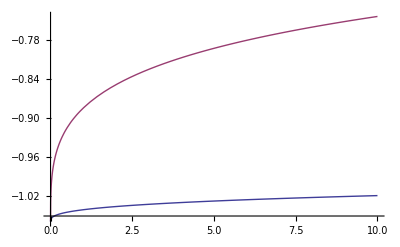

```mathematica
Plot[{toplot1,toplot2},{x,0,10}]
```